```mathematica
(*run waveguide.nb first*)
```

ReplaceAll::reps: {solsqx} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::nrnum1: The function value -1/ⅇ+2 (0.249937/.solsqx)+2 (0.25005/.solsqx) is not a real number when the arguments are {0.000150655,0.249901,0.249937,0.249937,0.249986,0.249937,0.249986,0.249986,0.25005,0.249937,0.249986,0.249986,0.25005,0.249986,0.25005,0.25005,0.250127}.

NDSolve::nrnum1: The function value -1/ⅇ+2 (0.249873/.solsqx)+2 (0.250099/.solsqx) is not a real number when the arguments are {0.000301311,0.249802,0.249873,0.249873,0.249972,0.249873,0.249972,0.249972,0.250099,0.249873,0.249972,0.249972,0.250099,0.249972,0.250099,0.250099,0.250254}.

General::stop: Further output of NDSolve::nrnum1 will be suppressed during this calculation.

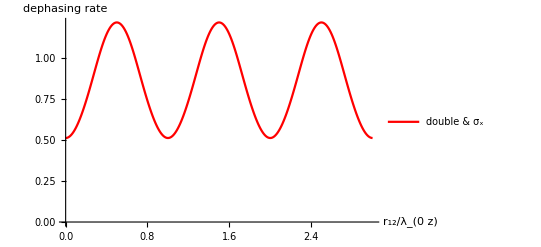

```mathematica
dphx=ListLinePlot[Table[{n,
δ=10^-7;di=n λ0z;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqx=NDSolve[{ρ'[t]==-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==initx,WhenEvent[Re[Evaluate[a[1,3][t]/.solsqx]+Evaluate[a[2,4][t]/.solsqx]+Evaluate[a[3,1][t]/.solsqx]+Evaluate[a[4,2][t]/.solsqx]][[1]]==1/E,dx=1/t]},slnn,{t,0,1000},MaxSteps->50000];dx},{n,0.0,3,0.01}],AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotStyle->Red,PlotLegends->LineLegend[{"double & σ_x"}]]
```

ReplaceAll::reps: {solsqdp} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::nbnum1: The function value 2 (0.176777-0.176777 ⅈ/.solsqdp)+2 (0.176777+0.176777 ⅈ/.solsqdp)==0.26013 is not True or False when the arguments are {0.,0.25+0. ⅈ,0.176777-0.176777 ⅈ,0.176777-0.176777 ⅈ,0.-0.25 ⅈ,0.176777+0.176777 ⅈ,0.25+0. ⅈ,«20»,-0.38577+0. ⅈ,0.232649-0.0249006 ⅈ,0.2938-0.38577 ⅈ,0.232649+0.0249006 ⅈ,0.232649+0.0249006 ⅈ,1.13577+0. ⅈ}.

NDSolve::nbnum1: The function value (0.176747-0.176726 ⅈ/.solsqdp)+(0.176747+0.176726 ⅈ/.solsqdp)+(0.1768-0.176779 ⅈ/.solsqdp)+(0.1768+0.176779 ⅈ/.solsqdp)==0.26013 is not True or False when the arguments are {0.0000997347,0.249964+0. ⅈ,0.176747-0.176726 ⅈ,0.176747-0.176726 ⅈ,0.0000292841-0.249962 ⅈ,«23»,0.232576-0.0247355 ⅈ,0.29362-0.385711 ⅈ,0.232576+0.0247355 ⅈ,0.232576+0.0247355 ⅈ,1.13548+0. ⅈ}.

NDSolve::nbnum1: The function value (0.176717-0.176676 ⅈ/.solsqdp)+(0.176717+0.176676 ⅈ/.solsqdp)+(0.176823-0.176782 ⅈ/.solsqdp)+(0.176823+0.176782 ⅈ/.solsqdp)==0.26013 is not True or False when the arguments are {0.000199469,0.249927+0. ⅈ,0.176717-0.176676 ⅈ,0.176717-0.176676 ⅈ,0.0000585501-0.249923 ⅈ,«23»,0.232503-0.0245705 ⅈ,0.293439-0.385651 ⅈ,0.232503+0.0245705 ⅈ,0.232503+0.0245705 ⅈ,1.13519+0. ⅈ}.

General::stop: Further output of NDSolve::nbnum1 will be suppressed during this calculation.

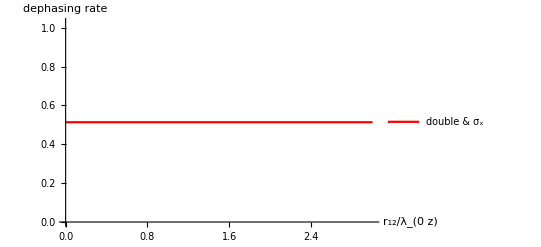

```mathematica
dphx=ListLinePlot[Table[{n,
δ=10^-7;di=n λ0z;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqx=NDSolve[{ρ'[t]==-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==initdp,WhenEvent[Re[Evaluate[a[1,3][t]/.solsqdp]+Evaluate[a[2,4][t]/.solsqdp]+Evaluate[a[3,1][t]/.solsqdp]+Evaluate[a[4,2][t]/.solsqdp]][[1]]==1/E*0.7071067811865475,dx=1/t]},slnn,{t,0,1000},MaxSteps->50000];dx},{n,0.0,3,0.01}],AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotStyle->Red,PlotLegends->LineLegend[{"double & σ_x"}]]
```

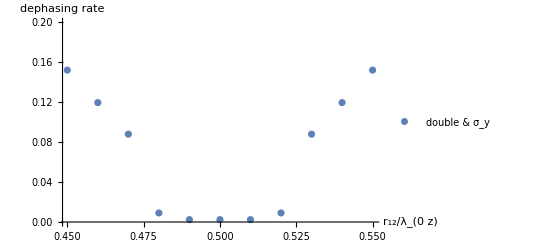

```mathematica
dphy=ListPlot[Table[{n,
di=n λ0z;δ=10^-7;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqy=NDSolve[{ρ'[t]==-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==inity,WhenEvent[Im[-Evaluate[a[1,3][t]/.solsqy]-Evaluate[a[2,4][t]/.solsqy]+Evaluate[a[3,1][t]/.solsqy]+Evaluate[a[4,2][t]/.solsqy]][[1]]<1/E ,dy=1/t]},slnn,{t,0,10000},MaxSteps->50000];dy},{n,0.45,0.55,0.01}],AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotLegends->LineLegend[{"double & σ_y"}],PlotRange->{0,0.2}]
```

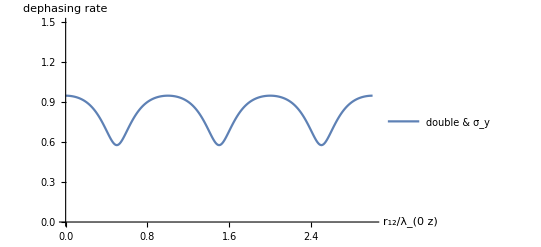

```mathematica
dphy=ListLinePlot[Table[{n,
di=n λ0z;δ=10^-7;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;

thy=NDSolve[{ρ'[t]==TH,ρ[0]==inity},slnn,{t,0,100},MaxSteps->50000];thy=NDSolve[{ρ'[t]==-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==inity,WhenEvent[Im[(-a[1,3][t]-a[2,4][t]+a[3,1][t]+a[4,2][t])/.thy][[1]]==1/E ,dy=1/t]},slnn,{t,0,10000},MaxSteps->50000];dy},{n,0,3,0.01}],AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotLegends->LineLegend[{"double & σ_y"}],PlotRange->{0,1.5}]
```

```mathematica
dphx=ListLinePlot[Table[{n,
di=n λ0z;δ=10^-7;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;thx=NDSolve[{ρ'[t]==-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==initx,WhenEvent[Re[Evaluate[a[1,3][t]/.thx]+Evaluate[a[2,4][t]/.thx]+Evaluate[a[3,1][t]/.thx]+Evaluate[a[4,2][t]/.thx]][[1]]==1/E,dx=1/t]},slnn,{t,0,10000},MaxSteps->50000];dx},{n,0.0,3,0.01}],AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotLegends->LineLegend[{"double & σ_y"}],PlotRange->{0,1.5}]
```

-Graphics-

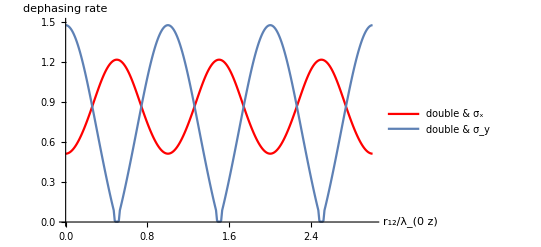

```mathematica
Show[{dphx,dphy},PlotRange->{0,1.5}]
```

```mathematica
Export["double-dphasing.csv",%]
```

double-dphasing.csv

```mathematica
sdph=Plot[{1/2 Exp[-2]+2Sin[2Pi ϕ]^2Sinh[1]Cosh[1],1/2 Exp[2]-Sin[2Pi ϕ]^2Sinh[2],1/2 Exp[-2],1/2 Exp[2]},{ϕ,0,1},AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotLegends->{"σ_x","σ_y","1/2e^(-2 r)","1/2e^(2  r)"}];
```

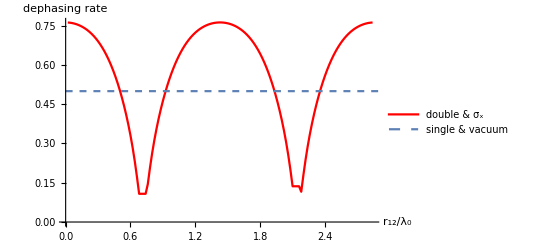

```mathematica
Show[{dphx,ListLinePlot[Table[{n,1/2 Exp[-2rr]},{n,0,3,0.01}],PlotStyle->Dashed,PlotLegends->LineLegend[{"single & vacuum"}]]}]
```

```mathematica
Export["vac.eps",%]
```

vac.eps

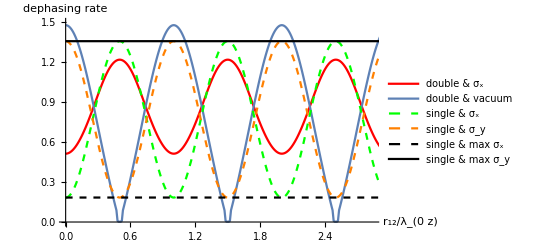

```mathematica
Show[{dphx,dphy,Plot[{1/2 Exp[-2rr]+2Sin[2Pi n/2]^2Sinh[rr]Cosh[rr],1/2 Exp[2 rr]-Sin[2Pi  n/2]^2Sinh[2 rr],1/2 Exp[-2 rr],1/2 Exp[2 rr]},{n,0,3},PlotStyle->{{Dashed,Green},{Dashed,Orange},{Dashed,Black},{Thick,Black}},PlotLegends->{"single & σ_x","single & σ_y","single & max σ_x","single & max σ_y"}],PlotRange->{{0,2.84},{0,1.5}}}]
```

```mathematica
Export["double.eps",%]
```

double.eps

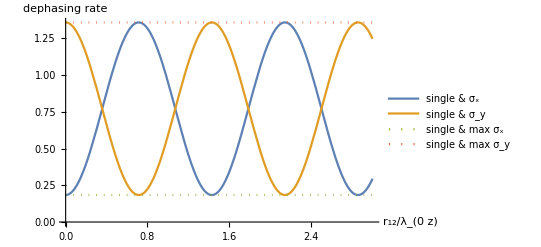

```mathematica
Plot[{1/2 Exp[-1]+2Sin[k0z n/2]^2Sinh[0.5]Cosh[0.5],1/2 Exp[1]-Sin[k0z n/2]^2Sinh[1],1/2 Exp[-1],1/2 Exp[1]},{n,0,3},PlotStyle->{Thick,Thick,Dotted,Dotted},PlotLegends->{"single & σ_x","single & σ_y","single & max σ_x","single & max σ_y"},AxesLabel->{"r_12/λ_(0  z)","dephasing rate"}]
```

```mathematica
Export["c:\\single.eps",%]
```

Export::noopen: Cannot open c:\single.eps.

$Failed

```mathematica
Import["single.eps"]
```

LinkObject::linkd: Unable to communicate with closed link LinkObject["C:\Program Files\Wolfram Research\Mathematica\11.0\SystemFiles\Converters\Binaries\Windows-x86-64\PDF.exe",3092,7].

$Failed

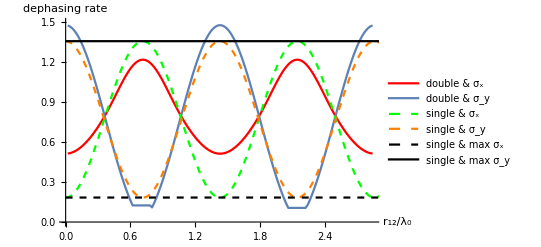

```mathematica
Directory[]
```

C:\Users\youji\OneDrive\Documents

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Jieyu You\Google Drive\multi atom

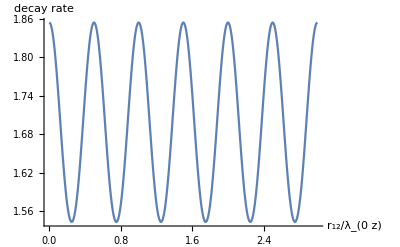

```mathematica
pd=ListLinePlot[Table[{n,
di=n λ0z;δ=10^-7;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;thee=NDSolve[{ρ'[t]==-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==initee,WhenEvent[Re[(((a[1,1][t]+a[2,2][t]-a[3,3][t]-a[4,4][t])/.thee)[[1]]+1/(2sh^2+1))/(1+1/(2sh^2+1))]==1/E,dy=1/(t)]},slnn,{t,0,1000},MaxSteps->50000];dy},{n,0,3,0.01}],AxesLabel->{"r_12/λ_(0  z)","decay rate"}]
```

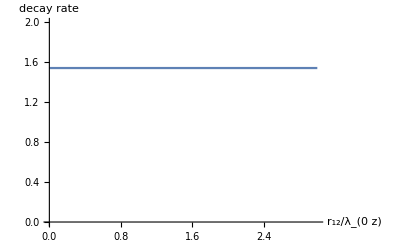

```mathematica
pds=ListLinePlot[Table[{n,
di=n λ0z;δ=10^-7;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqs=NDSolve[{ρs'[t]==sh ch γ12(σps.ρs[t].σps+σms.ρs[t].σms)-1/2(sh^2+1)(ρs[t].σps.σms+σps.σms.ρs[t]-2σms.ρs[t].σps)-1/2 sh^2(ρs[t].σms.σps+σms.σps.ρs[t]-2σps.ρs[t].σms ),ρs[0]==inits,WhenEvent[(Re[Evaluate[s[1,1][t]/.solsqs]-Evaluate[s[2,2][t]/.solsqs]][[1]]+1/(2sh^2+1))/(1+1/(2sh^2+1))==1/E,dy=1/(t)]},slnns,{t,0,30},MaxSteps->50000];dy},{n,0,3,0.01}],AxesLabel->{"r_12/λ_(0  z)","decay rate"},PlotRange->{0,2}]
```

```mathematica
Table[{n,
di=n λ0z;δ=10^-7;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqee=NDSolve[{ρ'[t]==-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==initee,WhenEvent[Re[(((a[1,1][t]+a[2,2][t]-a[3,3][t]-a[4,4][t])/.solsqee)[[1]]+1/(2sh^2+1))/(1+1/(2sh^2+1))]==1/E,dy=1/(t)]},slnn,{t,0,1000},MaxSteps->50000];dy},{n,0,3,0.01}];
```

```mathematica
Export["decay3.dat",%]
```

decay3.dat

```mathematica
Table[{n,
di=n λ0z;δ=10^-7;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqs=NDSolve[{ρs'[t]==sh ch γ12(σps.ρs[t].σps+σms.ρs[t].σms)-1/2(sh^2+1)(ρs[t].σps.σms+σps.σms.ρs[t]-2σms.ρs[t].σps)-1/2 sh^2(ρs[t].σms.σps+σms.σps.ρs[t]-2σps.ρs[t].σms ),ρs[0]==inits,WhenEvent[(Re[Evaluate[s[1,1][t]/.solsqs]-Evaluate[s[2,2][t]/.solsqs]][[1]]+1/(2sh^2+1))/(1+1/(2sh^2+1))==1/E,dy=1/(t)]},slnns,{t,0,30},MaxSteps->50000];dy},{n,0,3,0.01}];
```

```mathematica
Export["decay4.dat",%]
```

decay4.dat

```mathematica
ρs[t]/.solsqs/.t->1
```

{{{0.352085299367955,0},{0,0.647914700632045}}}

```mathematica
2sh^2+1
rr
```

1.54308

0.5

```mathematica
(Re[Evaluate[s[1,1][t]/.solsqs]-Evaluate[s[2,2][t]/.solsqs]][[1]]+1/(2sh^2+1))/(1+1/(2sh^2+1))/.t->0
```

1.

```mathematica
Tr[{{1,0},{0,-1}}.ρs[t]]
```

s[1,1][t]-s[2,2][t]

```mathematica
N[2sh^2+1]
```

1.54308

```mathematica
Tr[(2σ1p.σ1m-1).ρ[t]/.solsqee]/.t->1
```

0.318843

```mathematica
Tr[ρ[t].(σ[3,1]-σ[3,0])]
```

-a[1,5][t]-a[2,6][t]-a[3,7][t]-a[4,8][t]+a[5,1][t]+a[6,2][t]+a[7,3][t]+a[8,4][t]-a[9,13][t]-a[10,14][t]-a[11,15][t]-a[12,16][t]+a[13,9][t]+a[14,10][t]+a[15,11][t]+a[16,12][t]-a[17,21][t]-a[18,22][t]-a[19,23][t]-a[20,24][t]+a[21,17][t]+a[22,18][t]+a[23,19][t]+a[24,20][t]-a[25,29][t]-a[26,30][t]-a[27,31][t]-a[28,32][t]+a[29,25][t]+a[30,26][t]+a[31,27][t]+a[32,28][t]

```mathematica
ρ[t][[2^9,2^9]]
```

a[512,512][t]

```mathematica
dphx=ListLinePlot[Table[{n,
δ=10^-7;di= λ0z;Λ21=0.5Sin[k0z di ];γ12=Cos[k0z di ];Λ12=Λ21;γp12=1;
γp21=1;
γp11=γ12 ;
γp22=γ12 ;solsqx=NDSolve[{ρ'[t]==-sh ch(((1/2γp21+I Λp21)( σ2p.σ1p.ρ[t]+ ρ[t].σ2p.σ1p)+(1/2γp12+I Λp12)( σ1p.σ2p.ρ[t]+ ρ[t].σ1p.σ2p))+((1/2γp21-I Λp21)( σ2m.σ1m.ρ[t]+ ρ[t].σ2m.σ1m)+(1/2γp12-I Λp12)( σ1m.σ2m.ρ[t]+ ρ[t].σ1m.σ2m))-((1γp21+2I Λp21) σ2p.ρ[t].σ1p+(1γp12+2I Λp12) σ1p.ρ[t].σ2p+(γp11+2I Λp11)σ1p.ρ[t].σ1p+(1γp22+2I Λp22) σ2p.ρ[t].σ2p)-((1γp12 -2I Λp12)σ1m.ρ[t].σ2m+(1γp21-2I Λp21) σ2m.ρ[t].σ1m+(γp11-2I Λp11)σ1m.ρ[t].σ1m+(1γp22-2I Λp11) σ2m.ρ[t].σ2m))-1/2(sh^2+1)((ρ[t].σ1p.σ1m+γ12 ρ[t].σ1p.σ2m+γ12 ρ[t].σ2p.σ1m+ρ[t].σ2p.σ2m)+(σ1p.σ1m.ρ[t]+γ12 σ1p.σ2m.ρ[t]+γ12 σ2p.σ1m.ρ[t]+σ2p.σ2m.ρ[t])-2(σ1m.ρ[t].σ1p+γ12 σ1m.ρ[t].σ2p+γ12 σ2m.ρ[t].σ1p+σ2m.ρ[t].σ2p))-1/2 sh^2((ρ[t].σ1m.σ1p+γ12 ρ[t].σ1m.σ2p+γ12 ρ[t].σ2m.σ1p+ρ[t].σ2m.σ2p)+(σ1m.σ1p.ρ[t]+γ12 σ1m.σ2p.ρ[t]+γ12 σ2m.σ1p.ρ[t]+σ2m.σ2p.ρ[t])-2(σ1p.ρ[t].σ1m+γ12 σ1p.ρ[t].σ2m+γ12 σ2p.ρ[t].σ1m+σ2p.ρ[t].σ2m))-I Λ21( σ1p.σ2m.ρ[t]- ρ[t].σ1p.σ2m)-I Λ21(σ2p.σ1m.ρ[t]-ρ[t].σ2p.σ1m),ρ[0]==initx,WhenEvent[Re[Evaluate[a[1,3][t]/.solsqx]+Evaluate[a[2,4][t]/.solsqx]+Evaluate[a[3,1][t]/.solsqx]+Evaluate[a[4,2][t]/.solsqx]][[1]]==1/E,dx=1/t]},slnn,{t,0,1000},MaxSteps->50000];dx},{n,0.0,3,0.01}],AxesLabel->{"r_12/λ_(0  z)","dephasing rate"},PlotStyle->Red,PlotLegends->LineLegend[{"double & σ_x"}]]
```

```mathematica
Tr[ρ[t].(σ[1,1]-σ[1,0])]
```

-a[1,3][t]-a[2,4][t]+a[3,1][t]+a[4,2][t]